# Name - Vinay Kishor Roll no. - 20201459 Course - Bsc. (H) Computer Science Bisection methods in different forms:-

1 th iteration value is : 1.

Estimated error in 1th iteration is : 1.

2 th iteration value is : 1.5

Estimated error in 2th iteration is : 0.5

3 th iteration value is : 1.75

Estimated error in 3th iteration is : 0.25

4 th iteration value is : 1.625

Estimated error in 4th iteration is : 0.125

5 th iteration value is : 1.5625

Estimated error in 5th iteration is : 0.0625

6 th iteration value is : 1.59375

Estimated error in 6th iteration is : 0.03125

7 th iteration value is : 1.57813

Estimated error in 7th iteration is : 0.015625

8 th iteration value is : 1.57031

Estimated error in 8th iteration is : 0.0078125

9 th iteration value is : 1.57422

Estimated error in 9th iteration is : 0.00390625

10 th iteration value is : 1.57227

Estimated error in 10th iteration is : 0.00195313

11 th iteration value is : 1.57129

Estimated error in 11th iteration is : 0.000976563

12 th iteration value is : 1.5708

Estimated error in 12th iteration is : 0.000488281

13 th iteration value is : 1.57056

Estimated error in 13th iteration is : 0.000244141

14 th iteration value is : 1.57068

Estimated error in 14th iteration is : 0.00012207

1.57074

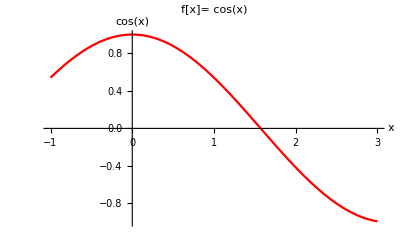

```mathematica
x0 = 0;
x1 = 2.0;
Nmax = 20;
eps = 0.0001;
f[x_] := Cos[x];
If[N[f[x0]*f[x1]]>0,
Print["Yours values do not satisfy the IVP so change the value."],
For[i = 1, i≤ Nmax, i++, m = (x0+x1)/2;
If[Abs[(x1-x0)/2]<eps,Return[m],
Print[i," th iteration value is : ", m];
Print["Estimated error in ", i, "th iteration is : ",(x1-x0)/2];
If[f[m]*f[x1]>0, x1 = m , x0 = m]]];
Print["Root is : ", m]
Print["Estimated error in ", i, "th iteration is :",(x1-x0)/2]]
Plot[f[x],{x,-1,3}, PlotRange->{-1,1},
PlotStyle->Red, PlotLabel->"f[x]=" f[x], AxesLabel->{x,f[x]}]
```

1 th iteration value is : 1.

Estimated error in 1th iteration is : 1.

2 th iteration value is : 0.5

Estimated error in 2th iteration is : 0.5

3 th iteration value is : 0.25

Estimated error in 3th iteration is : 0.25

4 th iteration value is : 0.125

Estimated error in 4th iteration is : 0.125

5 th iteration value is : 0.1875

Estimated error in 5th iteration is : 0.0625

6 th iteration value is : 0.21875

Estimated error in 6th iteration is : 0.03125

7 th iteration value is : 0.203125

Estimated error in 7th iteration is : 0.015625

8 th iteration value is : 0.195313

Estimated error in 8th iteration is : 0.0078125

9 th iteration value is : 0.199219

Estimated error in 9th iteration is : 0.00390625

10 th iteration value is : 0.201172

Estimated error in 10th iteration is : 0.00195313

11 th iteration value is : 0.202148

Estimated error in 11th iteration is : 0.000976563

12 th iteration value is : 0.20166

Estimated error in 12th iteration is : 0.000488281

13 th iteration value is : 0.201416

Estimated error in 13th iteration is : 0.000244141

14 th iteration value is : 0.201538

Estimated error in 14th iteration is : 0.00012207

0.201599

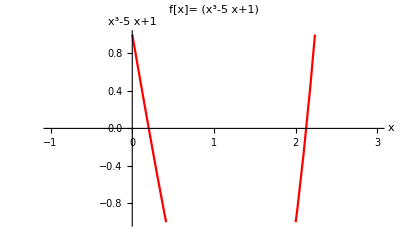

```mathematica
x0 = 0;
x1 = 2.0;
Nmax = 20;
eps = 0.0001;
f[x_] := x^3 - 5x + 1;
If[N[f[x0]*f[x1]]>0,
Print["Yours values do not satisfy the IVP so change the value."],
For[i = 1, i≤ Nmax, i++, m = (x0+x1)/2;
If[Abs[(x1-x0)/2]<eps,Return[m],
Print[i," th iteration value is : ", m];
Print["Estimated error in ", i, "th iteration is : ",(x1-x0)/2];
If[f[m]*f[x1]>0, x1 = m , x0 = m]]];
Print["Root is : ", m]
Print["Estimated error in ", i, "th iteration is :",(x1-x0)/2]]
Plot[f[x],{x,-1,3}, PlotRange->{-1,1},
PlotStyle->Red, PlotLabel->"f[x]=" f[x], AxesLabel->{x,f[x]}]
```

1 th iteration value is : 1.

Estimated error in 1th iteration is : 1.

2 th iteration value is : 0.5

Estimated error in 2th iteration is : 0.5

3 th iteration value is : 0.75

Estimated error in 3th iteration is : 0.25

4 th iteration value is : 0.625

Estimated error in 4th iteration is : 0.125

5 th iteration value is : 0.5625

Estimated error in 5th iteration is : 0.0625

6 th iteration value is : 0.53125

Estimated error in 6th iteration is : 0.03125

7 th iteration value is : 0.515625

Estimated error in 7th iteration is : 0.015625

8 th iteration value is : 0.523438

Estimated error in 8th iteration is : 0.0078125

9 th iteration value is : 0.519531

Estimated error in 9th iteration is : 0.00390625

10 th iteration value is : 0.517578

Estimated error in 10th iteration is : 0.00195313

11 th iteration value is : 0.518555

Estimated error in 11th iteration is : 0.000976563

12 th iteration value is : 0.518066

Estimated error in 12th iteration is : 0.000488281

13 th iteration value is : 0.517822

Estimated error in 13th iteration is : 0.000244141

14 th iteration value is : 0.5177

Estimated error in 14th iteration is : 0.00012207

0.517761

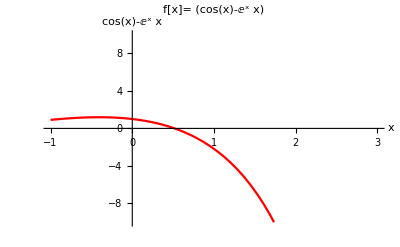

```mathematica
x0 = 0;
x1 = 2.0;
Nmax = 20;
eps = 0.0001;
f[x_] := Cos[x]-x*Exp[x];
If[N[f[x0]*f[x1]]>0,
Print["Yours values do not satisfy the IVP so change the value."],
For[i = 1, i≤ Nmax, i++, m = (x0+x1)/2;
If[Abs[(x1-x0)/2]<eps,Return[m],
Print[i," th iteration value is : ", m];
Print["Estimated error in ", i, "th iteration is : ",(x1-x0)/2];
If[f[m]*f[x1]>0, x1 = m , x0 = m]]];
Print["Root is : ", m]
Print["Estimated error in ", i, "th iteration is :",(x1-x0)/2]]
Plot[f[x],{x,-1,3}, PlotRange->{-10,10},
PlotStyle->Red, PlotLabel->"f[x]=" f[x], AxesLabel->{x,f[x]}]
```

#### Bisection Method:For Parameters Taken from user:-

```mathematica
x0 = Input["Enter first number :"];
x1 = Input["Enter second number :"];
Nmax =Input["Enter maximum number of iterations :"];
eps = Input["Enter a value of convergence parameter :"];
Print["x0 = ",x0];
Print["x1 = ",x1];
Print["Nmax = ",Nmax];
Print["epsilon = ",eps];
f[x_] := Cos[x];
If[N[f[x0]*f[x1]]>0,
Print["Yours values do not satisfy the IVP so change the value."],
For[i = 1, i≤ Nmax, i++, m = (x0+x1)/2;
If[Abs[(x1-x0)/2]<eps,Return[m],
Print[i," th iteration value is : ", m];
Print["Estimated error in ", i, "th iteration is : ",(x1-x0)/2];
If[f[m]*f[x1]>0, x1 = m , x0 = m]]];
Print["Root is : ", m]
Print["Estimated error in ", i, "th iteration is :",(x1-x0)/2]]
Plot[f[x],{x,-1,3}, PlotRange->{-1,1},
PlotStyle->Red, PlotLabel->"f[x]=" f[x], AxesLabel->{x,f[x]}]
```

x0 = 0

x1 = 2

Nmax = 20

epsilon = 1.×10^-6

1 th iteration value is : 1

Estimated error in 1th iteration is : 1

2 th iteration value is : 3/2

Estimated error in 2th iteration is : 1/2

3 th iteration value is : 7/4

Estimated error in 3th iteration is : 1/4

4 th iteration value is : 13/8

Estimated error in 4th iteration is : 1/8

5 th iteration value is : 25/16

Estimated error in 5th iteration is : 1/16

6 th iteration value is : 51/32

Estimated error in 6th iteration is : 1/32

7 th iteration value is : 101/64

Estimated error in 7th iteration is : 1/64

8 th iteration value is : 201/128

Estimated error in 8th iteration is : 1/128

9 th iteration value is : 403/256

Estimated error in 9th iteration is : 1/256

10 th iteration value is : 805/512

Estimated error in 10th iteration is : 1/512

11 th iteration value is : 1609/1024

Estimated error in 11th iteration is : 1/1024

12 th iteration value is : 3217/2048

Estimated error in 12th iteration is : 1/2048

13 th iteration value is : 6433/4096

Estimated error in 13th iteration is : 1/4096

14 th iteration value is : 12867/8192

Estimated error in 14th iteration is : 1/8192

15 th iteration value is : 25735/16384

Estimated error in 15th iteration is : 1/16384

16 th iteration value is : 51471/32768

Estimated error in 16th iteration is : 1/32768

17 th iteration value is : 102943/65536

Estimated error in 17th iteration is : 1/65536

18 th iteration value is : 205887/131072

Estimated error in 18th iteration is : 1/131072

19 th iteration value is : 411775/262144

Estimated error in 19th iteration is : 1/262144

20 th iteration value is : 823549/524288

Estimated error in 20th iteration is : 1/524288

Root is : 823549/524288

Estimated error in 21th iteration is :1/1048576

Null^2

-Graphics-